## Problem 2. b.

Real part of dielectric constant

```mathematica
ϵ1=1-(Ωp^2*(ω^2-ω0^2))/((ω^2-ω0^2)^2+ω^2/τ^2)
```

1-((ω^2-ω0^2) Ωp^2)/(ω^2/τ^2+(ω^2-ω0^2)^2)

imaginary part of dielectric constant

```mathematica
ϵ2=((Ωp^2*ω)/τ)/((ω^2-ω0^2)^2+ω^2/τ^2)
```

(ω Ωp^2)/(τ (ω^2/τ^2+(ω^2-ω0^2)^2))

Plot of real part

```mathematica
Plot[ϵ1/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,-10^17,10^17},Frame->True,Axes->False,FrameLabel->{"ω","ϵ_1"},LabelStyle->{Bold,16},PlotRange->{-15,15},PlotPoints->200]
```

-Graphics-

Zoomed in view of real part

```mathematica
Plot[ϵ1/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,2*10^16-10^15,2*10^16+10^15},Frame->True,Axes->False,FrameLabel->{"ω","ϵ_1"},LabelStyle->{Bold,16},PlotRange->{-15,15}]
```

-Graphics-

Plot of imaginary part

```mathematica
Plot[ϵ2/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,-10^17,10^17},Frame->True,Axes->False,FrameLabel->{"ω","ϵ_2"},LabelStyle->{Bold,16},PlotRange->{-20,20},PlotPoints->200]
```

-Graphics-

zoomed in view

```mathematica
Plot[ϵ2/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,2*10^16-10^15,2*10^16+10^15},Frame->True,Axes->False,FrameLabel->{"ω","ϵ_2"},LabelStyle->{Bold,16},PlotRange->{-20,20}]
```

-Graphics-

```mathematica
ϵ2/.{ω->2*10^16,ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15}//N
```

18.75

```mathematica
ϵ2/.ω->ω0
```

(τ Ωp^2)/ω0

Real part of index of refraction

```mathematica
nReal=Re[Sqrt[ϵ1+ⅈ*ϵ2]];
```

```mathematica
Plot[nReal/.{ω0->2*10^16,Ωp->5*10^15,τ->1 15*10^-15},{ω,2*10^16-1*10^15,2*10^16+1*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Real Part of Index of Refraction"},LabelStyle->{Bold,16},PlotRange->All]
```

-Graphics-

phase velocity, in units of c

```mathematica
vPhase=1/Re[Sqrt[ϵ1+ⅈ*ϵ2]];
```

```mathematica
Plot[vPhase/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,2*10^16-1*10^15,2*10^16+1*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Phase Velocity in Units of c"},LabelStyle->{Bold,16},PlotRange->All]
```

-Graphics-

group velocity, in units of c

```mathematica
vGroup=1/Re[D[ω*Sqrt[ϵ1+ⅈ*ϵ2],ω]];
```

```mathematica
Plot[vGroup/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,2.0*10^16-1*10^15,2.0*10^16+1*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Group Velocity in Units of c"},LabelStyle->{Bold,16},PlotRange->{-100,100},PlotPoints->200]
```

-Graphics-

```mathematica
Plot[vGroup/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,2.05*10^16-0.1*10^15,2.05*10^16+0.1*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Group Velocity in Units of c"},LabelStyle->{Bold,16},PlotRange->{-10,10},PlotPoints->200]
```

-Graphics-

far awar from resonance, the group velocity approaches 1

```mathematica
Plot[vGroup/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,15*10^16,15*10^18},Frame->True,Axes->False,FrameLabel->{"ω","Group Velocity in Units of c"},LabelStyle->{Bold,16},PlotRange->All,PlotPoints->200]
```

-Graphics-

## Problem 3

```mathematica
ϵbar=1-(Ωp^2/2)/(ω^2+ⅈ*ω/τ-(ω0+δ)^2)-(Ωp^2/2)/(ω^2+ⅈ*ω/τ-(ω0-δ)^2)
```

1-Ωp^2/(2 ((ⅈ ω)/τ+ω^2-(-δ+ω0)^2))-Ωp^2/(2 ((ⅈ ω)/τ+ω^2-(δ+ω0)^2))

Real part of dielectric constant

```mathematica
Plot[Re[ϵbar/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15}],{ω,-10^17,10^17},Frame->True,Axes->False,FrameLabel->{"ω","Re[ϵbar]"},LabelStyle->{Bold,16},PlotRange->{-15,15}]
```

-Graphics-

```mathematica
Plot[Re[ϵbar/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15}],{ω,2*10^16-10^15,2*10^16+10^15},Frame->True,Axes->False,FrameLabel->{"ω","Re[ϵbar]"},LabelStyle->{Bold,16},PlotRange->{-15,15}]
```

-Graphics-

Imaginary part of dielectric constant

```mathematica
Plot[Im[ϵbar/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15}],{ω,-10^17,10^17},Frame->True,Axes->False,FrameLabel->{"ω","Im[ϵbar]"},LabelStyle->{Bold,16},PlotRange->{-20,20}]
```

-Graphics-

```mathematica
Plot[Im[ϵbar/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15}]/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15},{ω,2*10^16-10^15,2*10^16+10^15},Frame->True,Axes->False,FrameLabel->{"ω","Im[ϵbar]"},LabelStyle->{Bold,16},PlotRange->{-20,20}]
```

-Graphics-

Real part of index of refraction

```mathematica
nReal=Re[Sqrt[ϵbar]];
```

```mathematica
Plot[nReal/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15},{ω,2*10^16-1*10^15,2*10^16+1*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Real Part of Index of Refraction"},LabelStyle->{Bold,16},PlotRange->All]
```

-Graphics-

Imaginary part of index of refraction

```mathematica
nIm=Im[Sqrt[ϵbar]];
```

```mathematica
Plot[nIm/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15},{ω,2*10^16-1*10^15,2*10^16+1*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Imaginary Part of Index of Refraction"},LabelStyle->{Bold,16},PlotRange->All]
```

-Graphics-

phase velocity, in units of c

```mathematica
vPhase=1/Re[Sqrt[ϵbar]];
```

```mathematica
Plot[vPhase/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15},{ω,2*10^16-1*10^15,2*10^16+1*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Phase Velocity in Units of c"},LabelStyle->{Bold,16},PlotRange->All]
```

-Graphics-

group velocity, in units of c.  The group velocity is significantly slowed down, to about 0.003 c.

```mathematica
vGroup=1/Re[D[ω*Sqrt[ϵbar],ω]];
```

```mathematica
Plot[vGroup/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15},{ω,2.0*10^16-0.01*10^15,2.0*10^16+0.05*10^15},Frame->True,Axes->False,FrameLabel->{"ω","Group Velocity in Units of c"},LabelStyle->{Bold,16},PlotRange->All,PlotPoints->200]
```

-Graphics-

The damping is reduced near the center of the lines for the case of the split resonance:

Damping at center of split resonance

```mathematica
damping=Im[Sqrt[ϵbar]]/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15,ω->2*10^16}
```

0.860005

Damping near center of unsplit resonance

```mathematica
ϵ=ϵ1+ⅈ*ϵ2//FullSimplify
```

1-(τ Ωp^2)/(ω (ⅈ+τ ω)-τ ω0^2)

```mathematica
damping2=Im[Sqrt[ϵ]]/.{ω0->2*10^16,Ωp->5*10^15,τ->15*10^-15,δ->0.09*10^15,ω->2*10^16}//N
```

2.98133

## Problem 7

here u represents ω(1-β Cos[θ])

```mathematica
Simplify[Integrate[ⅇ^(ⅈ*u*t)*Cos[ω0*t],{t,(-N1*π)/ω0,(N1*π)/ω0}],Assumptions->{N1∈Integers,N1>0}]
```

(2 (-1)^N1 u Sin[(N1 π u)/ω0])/(u^2-ω0^2)

```mathematica
f=2/(N1*π)*((x*Sin[N1*π*x])/(x^2-1))^2
```

(2 x^2 Sin[N1 π x]^2)/(N1 π (-1+x^2)^2)

plot of f(x) for N=1.  The main peak at x=1 is somewhat broad, with several side peaks.

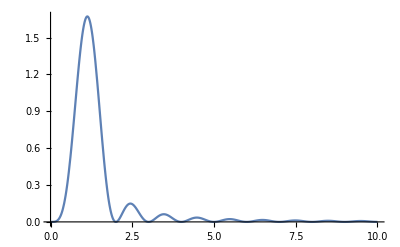

```mathematica
Plot[f/.N1->1,{x,0,10},PlotRange->All]
```

As N is increased,the main peak gets narrower and taller, as shown in the plots below.  The main peak is always at x=1

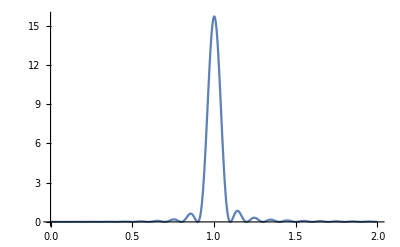

```mathematica
Plot[f/.N1->10,{x,0,2},PlotRange->All]
```

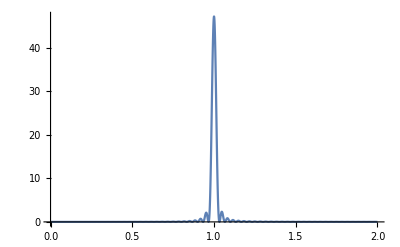

```mathematica
Plot[f/.N1->30,{x,0,2},PlotRange->All]
```

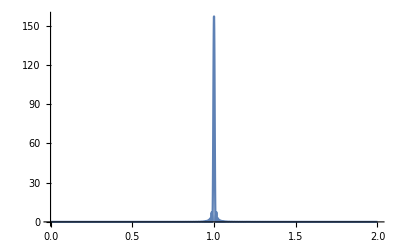

```mathematica
Plot[f/.N1->100,{x,0,2},PlotRange->All]
```